Part::partw: Part {1,2} of x[t] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

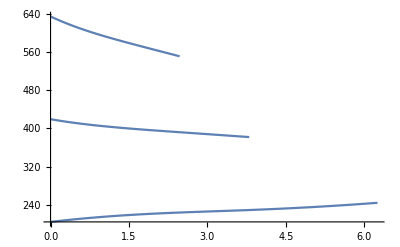

```mathematica
Clear[t]
r=1000; (*m, radius of cylinder*)
a = 9.81; (*m/s^2, radial acceleration at edge of cylinder*)
ω = Sqrt[a/r]; (*rad/s* angular velocity of cylinder*)
Clear[ω,r]
θ =45 Degree;
speed = 30; (*m/s, ball speed*)

RtoS[t_] := { (*change of basis from Rotating to Fixed (standard) reference frame*)
{-Sin[ω*t],-Cos[ω*t],0,r*Cos[ω*t]},
{Cos[ω*t],-Sin[ω*t],0,r*Sin[ω*t]},
{0,0,1,0},
{0,0,0,1}
};

StoR[t_]:=Simplify[Inverse[RtoS[t]]]; (*change of basis matrix from Fixed to Rotating reference frame*)

RtoS[t]//MatrixForm;
RtoS'[t]//MatrixForm;
StoR[t] //MatrixForm;

posRot = {0,1,0,1}; (*initial position in rotating refernce frame*)
vRot = {0,0,0,0}; (*initial velocity in rotating reference frame*)
Clear[vRot]

vAir[{x_,y_,z_,q_}]:=ω{-y,x,0,0}; (*velocity of air in absolute coordinates*)
Cd = 0.3; (*drag coeficient*)
ρ=1.2; (*kg/m^3, density of air*)
A = 0.004; (*m^2, cross sectional area of ball*)
m = 0.145; (*kg* mass of ball*)
ballAirV[p_,v_] := vAir[p]-v; (*airvelocity of ball as function of position and absolute velocity*)
  
dragForce[p_,v_]:=.5*Cd*A*ρ*Norm[ballAirV[p,v]]^2 *ballAirV[p,v]/Norm[ballAirV[p,v]];(*drag force on ball as function of position and absolute velocity*)
(*dragForce[p_,v_]:={0,0,0,0};*)
Clear[s]

nRadii = 1;
nAngles = 3;
minRad = 500;
maxRad = 500;
minAngle = -90 Degree;
maxAngle = 90 Degree;

Zeros[height_,width_]:=Table[0,{i,1,height},{j,1,width}] 
Zeros[size_]:=Zeros[size,size]
locations = Zeros[nRadii,nAngles];
rules = Zeros[nRadii,nAngles];
paths = Zeros[nRadii,nAngles];
velocities = Zeros[nRadii,nAngles];
radii = Array[#&,nRadii,{minRad,maxRad}];
angles = Array[#&,nAngles,{minAngle,maxAngle}];
For[i=1,i≤nRadii,i=i+1,
For[j=1,j≤nAngles,j=j+1,
{
r=radii[[i]],
ϕ=angles[[j]],
ω = Sqrt[a/r],
vRot=speed*{Cos[θ]Sin[ϕ],Sin[θ],Cos[θ]Cos[ϕ],0},
s=NDSolve[
{
m*x''[t]==dragForce[x[t],x'[t]],(*single differential equation*)
x[0]==RtoS[0].posRot,                               (*initial position in fixed frame*)
x'[0]==RtoS'[0].posRot+RtoS[0].vRot,(*initial velocity in fixed frame*)
WhenEvent[Norm[x[t][[{1,2}]]]>=r,{locations[[i,j]]={StoR[t].x[t],t},"StopIntegration"}] (*stop when the ball hits the edge of the cylinder, save the last time and position in end*)
},x,{t,0,1000}
],
rules[[i,j]] = s,
velocities[[i,j]]=Function[t,Evaluate[x'[t]/.rules[[i,j]]]],
paths[[i,j]]=Function[t,Evaluate[Evaluate[StoR[t]].x[t]/.rules[[i,j]]]]
}
]
]
PlotPath[{s_,end_}]:=ParametricPlot3D[s[t][[1,{1,2,3}]],{t,0,end},PlotStyle->{Thickness[.01],Green}];
PlotEnergy[{s_,end_}]:=Plot[.5*m*Norm[s[t]]^2,{t,0,end}];

Show[(PlotPath/@(Transpose[{Flatten[paths],Flatten[locations[[All,All,2]]]}]) )~Join~ {ContourPlot3D[(x)^2+(y-500)^2==500^2,{x,-100,100},{y,-10,500},{z,-10,70},Mesh->All,Boxed->False]},PlotRange->All,Boxed->False]
Show[PlotEnergy/@Transpose[{Flatten[velocities],Flatten[locations[[All,All,2]]]}],PlotRange->All]
```